# Teoria gier

## Ogólna koncepcja gry

Określenie graczy — skończoną liczbę graczy. Granicę skończonej liczby graczy.

Co mogą zrobić i kiedy i z jaką wiedzą.

Muszą wiedzieć jakie są konsekwencje ich działania. Czasami również preferencje na wynikach działań.

## Gra w postaci normalnej

### Gra w postaci normalnej

Zbiór graczy jest oznaczany przez ℐ i jest to skończony zbiór postaci ℐ={1,2,…,I}, gdzie I∈ℕ, jest liczbą graczy. Typowy elementy oznaczamy przez i∈ℐ.

Każdy gracz i∈ℐ posiada zbiór akcji A_i. W większości przypadków zbiór ten będzie skończony ale rozważymy również gry, które mają nieprzeliczalne zbiory akcji. Strategia graczy to funkcja, która zwraca akcję (strategia czysta) lub rozkład na akcjach (strategia mieszana). Zbiory strategii oznaczamy przez S_i dla gracza i∈ℐ.

Profil strategii to wektor zawierający strategie graczy a więc jest to wektor postaci s=(s_1,…,s_I)∈S=S_1×S_2×…×S_I.

Dla każdego gracza trzeba określić jego funkcję wypłaty. Funkcja wypłaty jest standardowo określona na profilach akcji ale przyjmuje się, że dla startegii jest zadana przez wartość oczekiwaną. Ściśle,

u_i:A=A_1×…×A_I→ℝ

lub dla profilu możemy zapisać u_i(a)∈ℝ. W przypadku profilu strategii s∈S określamy u_i(s) jako

u_i(s)=∑_(a∈A) p(s,a)·u_i(a),

gdzie p(s,a) jest prawdopodobieństwem wystąpienia profilu a akcji jeżeli gracze używają profilu strategii s.

Warto zauważyć, że z technicznego punktu widzenia, jeżeli gracz i gra przeciwko profilowi strategii s_-i to każdy wybór jego akcji jest wyborem pomiędzy zmiennymi losowymi. Przyjęcie, że wypłata gracza to średnia i założenie, że gracz maksymalizuje taką średnią jest relatywnie arbitralne. Może tutaj być znacznie więcej możliwości, np. wybór akcji z prawdopodobieństwem równym prawdopodobieństwu, że odpowiadająca zmienna losowa przyjmie największą wartość przy jednokrotnym teście (1-sampling).

Przez U_i będziemy oznaczali tensor I-wymiarowy (I-tensor) wypłat dla gracza i∈ℐ, który na miejscu (a_1,…,a_I) ma wypłatę u_i(a_1,…,a_I). W przypadku gier z dwoma graczami, tensor ten jest macierzą.

### Reprezentowanie gier w postaci normalnej dla dwóch graczy

W przypadku gier ze skończoną liczbą akcji i dwoma graczami, standardowa metoda to reprezentacja wypłat w postaci macierzy. Poniżej jest prosta funkcja, która dla zadanej liczby akcji i zadanego rozkładu losowego, tworzy losową grę

```mathematica
ClearAll[generateRandomBimatrixGame]
generateRandomBimatrixGame[𝒟_,size_]:=<|"player 1"->Partition[RandomVariate[𝒟,size/.List->Times],Last[size]],
"player 2"->Partition[RandomVariate[𝒟,size/.List->Times],Last[size]]
|>
```

Przykładowe wykorzytanie powyższej funkcji.

```mathematica
MatrixForm/@generateRandomBimatrixGame[NormalDistribution[0,2],{2,3}]
```

<|player 1→(-0.471639 | -0.182219 | -2.1858
1.05564 | -1.53391 | 1.5551),player 2→(-0.907183 | -0.642487 | 0.180207
2.25756 | 3.65316 | -2.73586)|>

```mathematica
MatrixForm/@generateRandomBimatrixGame[NormalDistribution[0,2],{5,2}]
```

<|player 1→(1.89145 | 2.43936
-3.0193 | -0.302316
-2.17466 | -0.232707
-3.46148 | -0.788505
0.299756 | 1.27786),player 2→(1.95435 | -1.85537
0.506709 | -0.18018
-1.86552 | -3.66394
1.75971 | 1.58028
-0.570715 | 1.12845)|>

```mathematica
MatrixForm/@generateRandomBimatrixGame[BinomialDistribution[5,1/2],{5,2}]
```

<|player 1→(3 | 1
4 | 3
4 | 3
2 | 2
4 | 2),player 2→(3 | 4
3 | 3
2 | 3
3 | 3
2 | 3)|>

### Reprezentacja gier w postaci normalnej dla I graczy

Powyższa reprezentacja gry nie jest specjalnie wygodna jeżeli chcemy mieć grę z większą skończoną liczbą graczy. Można tutaj wykorzystać wielowymiarowe listy. Poniżej jest podobna gra jak powyżej.

```mathematica
ClearAll[generateRandomGame]
generateRandomGame[𝒟_,size_]:=Module[{payoffs,k},
payoffs=Table[ArrayReshape[RandomVariate[𝒟,size/.List->Times],size],{k,1,Length[size]}];
<|Thread[Table["player "<>ToString[k],{k,1,Length[size]}]->payoffs]|>
]
```

Przykładowe wykorzystanie.

```mathematica
g1=generateRandomGame[BinomialDistribution[10,1/2],{2,3,4}]
```

<|player 1→{{{3,6,6,3},{3,4,4,4},{9,6,5,8}},{{3,3,2,4},{6,5,5,5},{5,7,5,5}}},player 2→{{{2,6,5,4},{6,5,4,7},{5,7,5,4}},{{5,7,5,6},{6,4,6,5},{6,5,6,5}}},player 3→{{{6,3,7,5},{4,5,4,7},{5,3,7,4}},{{3,6,4,6},{4,4,4,7},{4,6,4,5}}}|>

```mathematica
MatrixForm/@g1
```

<|player 1→((3
6
6
3) | (3
4
4
4) | (9
6
5
8)
(3
3
2
4) | (6
5
5
5) | (5
7
5
5)),player 2→((2
6
5
4) | (6
5
4
7) | (5
7
5
4)
(5
7
5
6) | (6
4
6
5) | (6
5
6
5)),player 3→((6
3
7
5) | (4
5
4
7) | (5
3
7
4)
(3
6
4
6) | (4
4
4
7) | (4
6
4
5))|>

```mathematica
g2=generateRandomGame[BinomialDistribution[10,1/2],{2,3,4,3,2,5,2,3}]
```

<|player 1→1,player 2→{{{1},{{1},2,{{{{{6,7,8},{4,7,3}},{{4,5,4},{6,5,3}},{{6,3,5},{3,4,7}},{{4,2,6},{4,7,4}},{{6,5,5},{5,4,8}}},{1}},{1},{1}}},{1}},1},4,1,player 8→{{{1},{1},{1}},{{1},{1},{1}}}|>
 |  |  |  |

```mathematica
g2["player 1"]//Short[#,4]&
```

{{{«1»},{«1»},{«1»}},{{«1»},«1»,{{{{{{4,6,4},{3,6,5}},{{4,3,7},{3,2,6}},{{3,7,5},{7,6,7}},{{2,5,4},{3,6,6}},{{5,2,5},{6,7,5}}},{{{5,5,6},{5,5,4}},{{7,7,6},{5,5,5}},{{5,7,4},{7,6,8}},{{6,7,8},{2,4,6}},{{5,4,4},{6,4,3}}}},«1»,{{{{4,6,4},{4,6,4}},«3»,{{6,5,5},{4,8,5}}},{«1»}}},{«1»},{«1»},{«1»}}}}

### Obliczanie wypłat

Jeżeli mamy już zdefiniowaną grę, to można bardzo łatwo wydobyć pojedyncze wypłaty dla akcji

```mathematica
g1["player 2"]⟦2,3,1⟧
```

6

lub profile wypłat dla profili akcji

```mathematica
g1[#]⟦2,3,1⟧&/@Keys[g1]
```

{3,6,3}

Warto jednak zdefniować funkcję, która pozwoli obliczać profile wypłat dla profili strategii (nie koniecznie czystych). W przypadku gier z dwoma macierzami wypłat obliczanie profili wypłat jest relatywnie proste. Jeżeli U_1 jest macierzą wypłat dla gracza pierwszego i U_2 jest macierzą wypłat dla gracza drugiego a gracze grają profil strategii (s_1,s_2) to wypłaty są zadane dla pierwszego gracza

u_1(s_1,s_2)=s_1^T·U_1·s_2

i podobnie dla gracza drugiego a więc

u_2(s_1,s_2)=u_1^T·U_2·u_2.

W przypadku gier dla wielu graczy wypłaty są działaniem I-tensorów na wektorze strategii (s_1,…,s_I) w następujący sposób

u_i(s_1,…,s_I)=∑_(j_1,…,j_I) (∏_(k=1)^I s_(k j_k))·u_i(a_j_1,…,a_(j I)).

Poniżej jest prosta funkcja, która implementuje powyższe obliczenia.

```mathematica
ClearAll[getPayoff]
getPayoff[game_?(Head[#["player 1"]]===List&),s_List]:=Table[Total@Flatten[game[key] Outer[Times,Sequence@@s]],{key,Keys[game]}]
```

Poniżej definiujemy prostą grę dla dwóch graczy i sprawdzamy czy powyższa funkcja rzeczywiście działa poprawnie.

```mathematica
g3=generateRandomGame[BinomialDistribution[5,1/2],{2,3}]
```

<|player 1→{{5,2,3},{2,3,4}},player 2→{{3,1,2},{2,4,1}}|>

```mathematica
MatrixForm/@g3
```

<|player 1→(5 | 2 | 3
2 | 3 | 4),player 2→(3 | 1 | 2
2 | 4 | 1)|>

```mathematica
s={{1/2,1/2},{1/2,1/4,1/4}};
getPayoff[g3,s]
```

{13/4,9/4}

Możemy manulanie sprawdzić czy otrzymane wyniki zgadzają się w prostym przykładzie.

```mathematica
s⟦1⟧.g3["player 1"].s⟦2⟧
```

13/4

```mathematica
s⟦1⟧.g3["player 2"].s⟦2⟧
```

9/4

I przykład dla większej gry.

```mathematica
g1=generateRandomGame[BinomialDistribution[10,1/2],{2,3,4}]
```

<|player 1→{{{3,5,6,5},{5,4,3,6},{6,6,5,5}},{{3,7,7,4},{6,8,6,6},{5,4,5,5}}},player 2→{{{6,3,7,5},{6,3,3,7},{2,6,5,6}},{{5,4,4,5},{6,6,6,6},{3,8,3,5}}},player 3→{{{6,4,5,8},{6,8,4,6},{4,4,3,4}},{{4,4,5,5},{7,5,4,5},{4,3,5,4}}}|>

```mathematica
MatrixForm/@g1
```

<|player 1→((3
5
6
5) | (5
4
3
6) | (6
6
5
5)
(3
7
7
4) | (6
8
6
6) | (5
4
5
5)),player 2→((6
3
7
5) | (6
3
3
7) | (2
6
5
6)
(5
4
4
5) | (6
6
6
6) | (3
8
3
5)),player 3→((6
4
5
8) | (6
8
4
6) | (4
4
3
4)
(4
4
5
5) | (7
5
4
5) | (4
3
5
4))|>

```mathematica
s = {{1,1}/2,{2,1,1}/4,{1,1,1,1}/4};
getPayoff[g1,s]
```

{165/32,159/32,79/16}

### Reprezentacja gier, gdzie wypłaty zależą od statystyk obliczanych na profilu strategii

Jest sporo ciekawych gier, gdzie wypłaty graczy zależą jedynie od statystyki od danego profilu. Przykładowo, tzw. minority game, to gra dla nieparzystej liczby graczy,  w której każdy gracz wybiera jedną z dwóch dróg. Wszyscy gracze, którzy znaleźli się na drodzę, którą wybrała mniejszość otrzymują wypłatę 1 podczas gdy gracze, którzy wybrali drogę wybraną przez większość otrzymują -1. Wypłata gracza zależy tutaj jedynie od liczby graczy wybierających dane drogi a nie akcji poszczególnych graczy. Warto zauważyć, że liczba równowag Nasha w strategiach czystych wynosi tutaj 2·2^((n-1)/2).

### Reprezentacja gier, gdzie wypłaty są zadane funkcjami

Poniżej jest funkcja, która zapewnia reprezentację gier bezpośrednio przy pomocy funkcji. Argumentem są tutaj czyste funkcje a nie wzory określające funkcje.

```mathematica
ClearAll[gameFromFunctions]
gameFromFunctions[u_List,vars_List]:=Append[<|Thread[Table["player "<>ToString[k],{k,1,Length[u]}]->u]|>,"variables"->vars]
```

Słabością powyższej funkcji jest brak dokładnego sprawdzania struktury argumentu ale można to dodać. Inny problem to z założenia pomiamy definicję zbioru strategii a więc nie wiemy gdzie jest zdefiniowana dana funkcja.

```mathematica
h1=gameFromFunctions[{(Sin[x+y]),a x y},{x,y}]
```

<|player 1→Sin[x+y],player 2→a x y,variables→{x,y}|>

Podobnie jak powyżej warto zdefiniować funkcję, która oblicza wypłaty dla profilu strategii. Tutaj jednak strategia mieszana to rozkład na dziedzinie danej funkcji. Podobnie jak powyżej teoretycznie powinniśmy sprawdzać dziedziny funkcji wypłat. Poniżej założenie jest takie, że dziedzina jest zadana przez rozkład ale to prawdopodobnie nie jest optymalne.

```mathematica
getPayoff[g_?(MemberQ[Keys[#],"variables"]&),s_List]:=Module[{vars,𝒦,keys,den,dom},
keys=Most@Keys[g];
vars=g["variables"];
dom=Sequence@@Table[{vars⟦𝒦⟧,-Infinity,Infinity},{𝒦,1,Length[vars]}];
den=Times@@Table[PDF[s⟦𝒦⟧,vars⟦𝒦⟧],{𝒦,1,Length[keys]}];
Table[
Integrate[Evaluate[g[keys⟦𝒦⟧] den],Evaluate[dom]],
{𝒦,1,Length[keys]}]
]
```

Przykładowe wykorzystanie powyższej funkcji dla zdefiniowanej poprzednio gry.

```mathematica
getPayoff[h1,{NormalDistribution[1,1],HalfNormalDistribution[1/2]}]
```

{ⅇ^(-1/2-π) (Cos[1] Erfi[√π]+Sin[1]),2 a}

### Wizualizacja gier

W istocie interesuje nas wizualizacja przestrzeni wypłat. Jest oczywiste, że możemy to zrobić jedynie dla gier z liczbą graczy nie większą niż 3. Poniżej jest prosta funkcja dla gier z dwoma graczami i dwoma akcjami. Dla większych gier również jest to możliwe ale wymaga innego programowania.

```mathematica
ClearAll[visualizeGame]
visualizeGame[g_?((Length[#]==2)&)]:=Module[{x,y},
ParametricPlot[
getPayoff[g,{{x,1-x},{y,1-y}}],
{x,0,1},{y,0,1},PlotTheme->"Scientific",PlotRange->All,FrameLabel->Keys[g],
GridLines->{Flatten[Join[g["player 1"],g["player 2"]]],Flatten[Join[g["player 1"],g["player 2"]]]}
]
]
```

Proste wykorzystnie powyższej funkcji.

```mathematica
g1=generateRandomGame[BinomialDistribution[10,1/2],{2,2}]
MatrixForm/@%
```

<|player 1→{{5,3},{5,5}},player 2→{{7,5},{4,5}}|>

<|player 1→(5 | 3
5 | 5),player 2→(7 | 5
4 | 5)|>

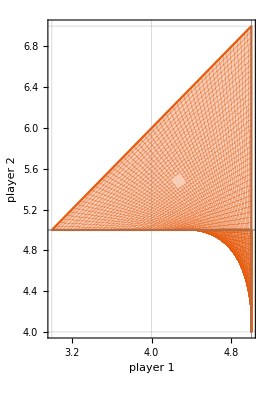

```mathematica
visualizeGame[g1]
```

Funkcja do wizualizacji gier dla dwóch graczy przy dowolnej skończonej liczbie akcji wymaga wizualizacji zbiorów postaci f(S), gdzie f:ℝ^(dim(A))→ℝ^2.